```mathematica
DSolve[y'[x]==Sin[5x],y[x],x]
```

{{y[x]→C[1]-1/5 Cos[5 x]}}

```mathematica
DSolve[x^2*y'[x]==y[x]-y[x]*x,y[x],x]
```

{{y[x]→(ⅇ^(-1/x) C[1])/x}}

```mathematica
DSolve[{x^2*y'[x]==y[x]-y[x]*x,y[1]==1/E},y[x],x]
```

{{y[x]→ⅇ^(-1/x)/x}}

```mathematica
DSolve[y''[x]+5y'[x]+2y[x]==0,y[x],x]
```

{{y[x]→ⅇ^((-5/2-(√17)/2) x) C[1]+ⅇ^((-5/2+(√17)/2) x) C[2]}}

```mathematica
DSolve[{y''[x]+5y'[x]+2y[x]==0,y[0]==5,y'[0]==10},y[x],x]
```

{{y[x]→-5/34 (-17 ⅇ^((-5/2-(√17)/2) x)+9 √17 ⅇ^((-5/2-(√17)/2) x)-17 ⅇ^((-5/2+(√17)/2) x)-9 √17 ⅇ^((-5/2+(√17)/2) x))}}

```mathematica
a=NDSolve[{y''[x]+x*y[x]==0,y[0]==1,y[1]==1},y[x],{x,0,10}]
```

{{y[x]→InterpolatingFunction[{{0.,10.}},<>][x]}}

```mathematica
Evaluate[y[x]/.a]
```

{InterpolatingFunction[{{0.,10.}},<>][x]}

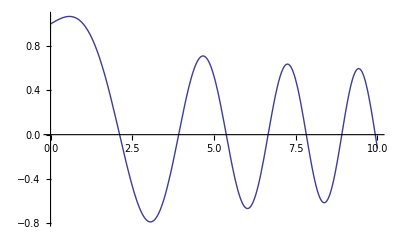

```mathematica
Plot[Evaluate[y[x]/.a],{x,0,10}]
```

```mathematica
b=NDSolve[{y''[t]+(y'[t]+1)^2*y'[t]+y[t]==0,y[0]==1,y'[0]==0},y[t],{t,0,10}]
```

{{y[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

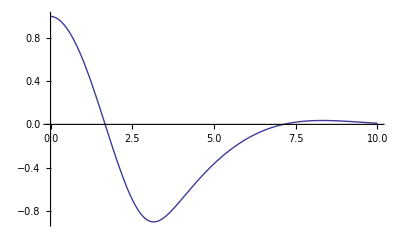

```mathematica
Plot[Evaluate[y[t]/.b],{t,0,10}]
```

```mathematica
c=NDSolve[{y''[x]+0.3*y'[x]+Sin[y[x]]==0,y[0]==2,y'[0]==0},y[x],{x,0,30}]
```

{{y[x]→InterpolatingFunction[{{0.,30.}},<>][x]}}

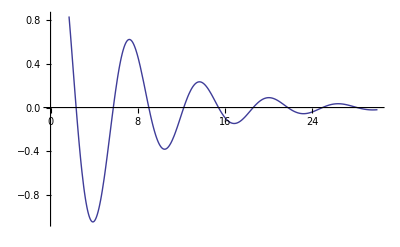

```mathematica
Plot[Evaluate[y[x]/.c],{x,0,30}]
```

```mathematica
DSolve[Vo*E^(j*ω*t)==L*Q''[t]+ R*Q'[t]+(Q[t]/C),Q[t],t]
```

{{Q[t]→-(2 C L Vo (√C ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) R-√C ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) R+ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) √(-4 L+C R^2)+ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) √(-4 L+C R^2)+2 √C ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) j L ω-2 √C ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) j L ω))/(√(-4 L+C R^2) (-√C R+√(-4 L+C R^2)-2 √C j L ω) (√C R+√(-4 L+C R^2)+2 √C j L ω))+ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)) C[1]+ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)) C[2]}}

```mathematica
DSolve[Vo*E^(j*ω*t)==i[t]*R+(i[t])^2/2C+L*i'[t],i[t],t]
```

{{i[t]→(2 L (C[1] ((ⅈ^(-R/(j L ω)) C ⅇ^(-(R t)/(2 L)+j t ω) Vo (BesselI[-1-R/(j L ω),(√2 √(C ⅇ^(j t ω) Vo))/(j L ω)]+BesselI[1-R/(j L ω),(√2 √(C ⅇ^(j t ω) Vo))/(j L ω)]) Gamma[1-R/(j L ω)])/(2 √2 L √(C ⅇ^(j t ω) Vo))-1/(2 L)ⅈ^(-R/(j L ω)) ⅇ^(-(R t)/(2 L)) R BesselI[-R/(j L ω),(√2 √(C ⅇ^(j t ω) Vo))/(j L ω)] Gamma[1-R/(j L ω)])+(ⅈ^(R/(j L ω)) C ⅇ^(-(R t)/(2 L)+j t ω) Vo (BesselI[-1+R/(j L ω),(√2 √(C ⅇ^(j t ω) Vo))/(j L ω)]+BesselI[1+R/(j L ω),(√2 √(C ⅇ^(j t ω) Vo))/(j L ω)]) Gamma[1+R/(j L ω)])/(2 √2 L √(C ⅇ^(j t ω) Vo))-1/(2 L)ⅈ^(R/(j L ω)) ⅇ^(-(R t)/(2 L)) R BesselI[R/(j L ω),(√2 √(C ⅇ^(j t ω) Vo))/(j L ω)] Gamma[1+R/(j L ω)]))/(C (ⅈ^(-R/(j L ω)) ⅇ^(-(R t)/(2 L)) BesselI[-R/(j L ω),(√2 √(C ⅇ^(j t ω) Vo))/(j L ω)] C[1] Gamma[1-R/(j L ω)]+ⅈ^(R/(j L ω)) ⅇ^(-(R t)/(2 L)) BesselI[R/(j L ω),(√2 √(C ⅇ^(j t ω) Vo))/(j L ω)] Gamma[1+R/(j L ω)]))}}